```mathematica
Print["SaveFigures: ",SetterBar[Dynamic[SaveFigures],{True->"On",False->"Off"}]]
```

SaveFigures:  |

## Initialization

### Packages, Paths, common options

```mathematica
SetOptions[$FrontEnd,CommonDefaultFormatTypes->{"Output"->StandardForm}];
If[FileExistsQ["~/home-fnal/algebra/packages"],BaseDir="~/home-fnal",BaseDir="~"];
SetDirectory[BaseDir<>"/papers/sterile-nu/sim"];
$Path=Append[$Path,BaseDir<>"/algebra/packages"];
<<KPTools.m;

(* Taken from http://forums.wolfram.com/mathgroup/archive/1999/Apr/msg00028.html (slightly modified) *)
JHEPPlot[grObj_Graphics]:=Module[{fulopts,tcklst,th=0.004},
fulopts=FullOptions[grObj];
tcklst=FrameTicks/.fulopts/.{loc_,lab_,len:{_,_},{sty:___}}:>{loc,lab,2*len,{Directive[sty,Thickness[th]]}};
grObj/.Graphics[prims_,(opts__)?OptionQ]:>Graphics[prims,FrameTicks->tcklst,FrameTicksStyle->Thickness[th],FrameStyle->Thickness[th],opts]
];
```

### Reading GLoBES event rate files

```mathematica
glbSignalTot[Data_List]:=Transpose[{Data⟦1,1,All,1⟧,Plus@@Data⟦1,All,All,2⟧}];
glbBGTot[Data_List]:=Transpose[{Data⟦2,1,All,1⟧,Plus@@Data⟦2,All,All,2⟧}];
glbSignalBGTot[Data_List]:=Transpose[{Data⟦1,1,All,1⟧,(Plus@@Data⟦1,All,All,2⟧)+(Plus@@Data⟦2,All,All,2⟧)}];
```

## Combined analysis

### Appearance experiments and 3+1 fit

```mathematica
DataFiles="3-3p1/dm41th14th24-"<>#<>".dat.gz"&/@{"lsnd","mb","mbanti","lsnd-mbanti","nevid","nevid-nominos","app","disapp","nevid-app","nevid-disapp"(*,"sbl","karmen","nomad","cdhs","atm","minos"*)};
DataFiles="3-3p1/dm41th14th24-"<>#<>".dat.gz"&/@{"e776-nosc-bg"};
ThetaEffMuE[th14_,th24_]:=Module[{Ue4,Uμ4},
Ue4=Sin[th14];
Uμ4=Cos[th14]*Sin[th24];
Return[4.Abs[Ue4]^2Abs[Uμ4]^2];
];
For[i=1,i≤Length[DataFiles],i++,
Data[i]=Cases[Import[DataFiles⟦i⟧,"Table"],{Repeated[_?NumericQ]}];
Data[i]=Flatten[{#⟦1;;-3⟧,Min[#⟦-2⟧,#⟦-1⟧]}]&/@Data[i];
logdmsqMin[i]=Min[Data[i]⟦All,1⟧];
logdmsqMax[i]=Max[Data[i]⟦All,1⟧];
logth14Min[i]=Min[Data[i]⟦All,2⟧];
logth14Max[i]=Max[Data[i]⟦All,2⟧];
logth24Min[i]=Min[Data[i]⟦All,3⟧];
logth24Max[i]=Max[Data[i]⟦All,3⟧];
Data[i]=Sort[{#⟦1⟧,Log10[ThetaEffMuE[10^#⟦2⟧,10^#⟦3⟧]],#⟦4⟧}&/@Data[i]];
DataInterpol[i]=Interpolation[Data[i],InterpolationOrder->1];
Chi2Min[i]=Min[Data[i]⟦All,-1⟧];
logthMin[i]=Min[Data[i]⟦All,2⟧];
logthMax[i]=Max[Data[i]⟦All,2⟧];
];
```

```mathematica
(* Use a more sophisticated conversion from Subscript[θ, 14], Subscript[θ, 24] for those experiments which are sensitive to both of them independently.
We use: x=sin 2 Subscript[θ, 14], c = sin 2 Subscript[θ, eff] = sin 2 Subscript[θ, 14] sin Subscript[θ, 24] => Subscript[θ, 24] = arcsin(c/x), Subscript[θ, 14] = 0.5 arcsin x *)
Clear[x,j];
For[i=1,i≤Length[DataFiles],i++,
If[!StringMatchQ[DataFiles⟦i⟧,RegularExpression[".*(evid|app|minos).*"]],
Continue[];
];
Data[i]=Cases[Import[DataFiles⟦i⟧,"Table"],{Repeated[_?NumericQ]}];
Data[i]=Flatten[{#⟦1;;-3⟧,Min[#⟦-2⟧,#⟦-1⟧]}]&/@Data[i];
DataInterpolFull[i]=Interpolation[Data[i],InterpolationOrder->1];
DataInterpol[i]=(FindMinimum[DataInterpolFull[j][#1,Clip[Log10[0.5ArcSin[x]],{logth14Min[i],logth14Max[i]}],Clip[Log10[ArcSin[Sqrt[10^#2]/x]],{logth24Min[i],logth24Max[i]}]],{x,10^(#2/4),-1,1}]⟦1⟧&)/.{j->i}
];
```

```mathematica
MyContours={χ2[2,0.1],χ2[2,0.01]};
MyStyles={
{Directive[Thick,Black],Directive[Thick,Black,Dashed]},
{Directive[Thick,Blue],Directive[Thick,Blue,Dashed]},
{Directive[Thick,RGBColor[0,0.5,0]],Directive[Thick,RGBColor[0,0.5,0],Dashed]},
{{Directive[Black],Directive[Black,Dashed]},{GrayLevel[0.7],Red,None}},
{Directive[Thick,Blue],Directive[Thick,Blue,Dashed]},
{Directive[Blue],Directive[Blue,Dashed]},
{{Directive[Black],Directive[Black,Dashed]},{GrayLevel[0.7],Red,None}},
{Directive[Thick,Blue],Directive[Thick,Blue,Dashed]},
{Directive[Thick,Blue],Directive[Thick,Blue,Dashed]},
{Directive[Thick,RGBColor[0,0.5,0]],Directive[Thick,RGBColor[0,0.5,0],Dashed]},

{Directive[Thick,Blue],Directive[Thick,Blue,Dashed]},
{Directive[Thick,Blue],Directive[Thick,Blue,Dashed]},
{Directive[Thick,Blue],Directive[Thick,Blue,Dashed]},
{Directive[Thick,Blue],Directive[Thick,Blue,Dashed]},
{Directive[Thick,Blue],Directive[Thick,Blue,Dashed]},
{Directive[Thick,Blue],Directive[Thick,Blue,Dashed]}
};
For[i=1,i≤Length[DataFiles],i++,
If[Head[MyStyles⟦i,1⟧]===List,
MyPlot[i]=ContourPlot[DataInterpol[i][logdmsq,logth]-Chi2Min[i],{logth,logthMin[i],logthMax[i]},{logdmsq,logdmsqMin[i],logdmsqMax[i]},Contours->MyContours,ContourShading->MyStyles⟦i,2⟧,ContourStyle->MyStyles⟦i,1⟧],
(* Else *)
MyPlot[i]=ContourPlot[DataInterpol[i][logdmsq,logth]-Chi2Min[i],{logth,logthMin[i],logthMax[i]},{logdmsq,logdmsqMin[i],logdmsqMax[i]},Contours->MyContours,ContourShading->False,ContourStyle->MyStyles⟦i⟧]
];
];
```

#### E776

Run above code to load E776 data file, then run the following

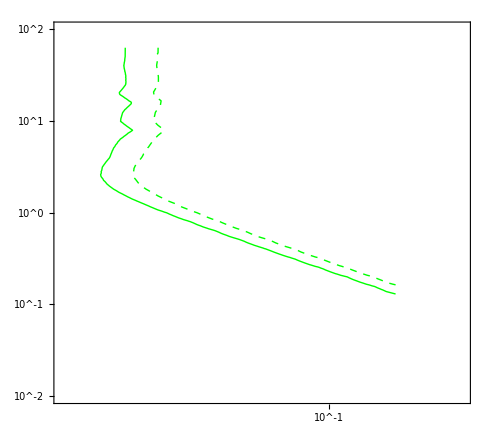

```mathematica
(* NOTE: E776 reference: http://dx.doi.org/10.1103/PhysRevLett.68.274 *)
Show[MyPlot[1]/.Black->Green,
PlotRange->{{-3,0},{-2,2}},ImageSize->490,AspectRatio->.9,ImagePadding->{{140,15},{70,25}},FrameTicks->{LogTicks[-10,10],LogTicks[-5,5],LogTicksNoLabel[-10,10],LogTicksNoLabel[-5,5]},Prolog->{Inset[Import["0-code/glb/e776/data/E776-binned.pdf"]⟦1⟧,Scaled[{.44,.45}]]}]
```

31.0815

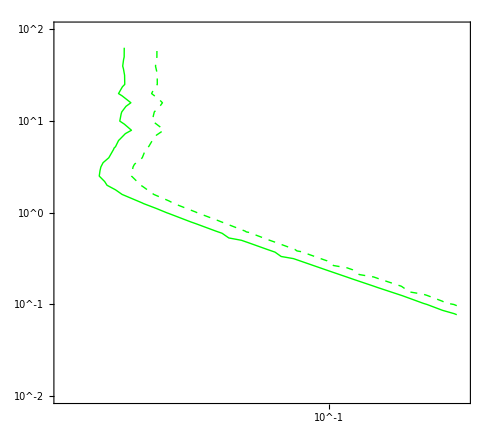

```mathematica
MyData=Cases[Import["3-3p1/e776-2flavor.dat.gz"],{Repeated[_?NumericQ]}];
Min[MyData⟦All,3⟧]
Show[ListContourPlot[{Log10[Sin[2 10^#⟦2⟧]^2],#⟦1⟧,Min[#⟦3⟧,#⟦4⟧]}&/@MyData,Contours->%+MyContours,ContourShading->False,ContourStyle->MyStyles⟦1⟧/.Black:>Green],
PlotRange->{{-3,0},{-2,2}},ImageSize->490,AspectRatio->.9,ImagePadding->{{140,15},{70,25}},FrameTicks->{LogTicks[-10,10],LogTicks[-5,5],LogTicksNoLabel[-10,10],LogTicksNoLabel[-5,5]},Prolog->{Inset[Import["0-code/glb/e776/data/E776-binned.pdf"]⟦1⟧,Scaled[{.44,.45}]]}]
```

673.751

ListContourPlot::gmat: {{-3., -1.8, 673.751}} is not a rectangular array larger than 2 x 2.

ListContourPlot[{{-3.,-1.8,673.751}},Contours→{678.356,682.961},PlotRange→Full,ContourShading→False,ContourStyle→GrayLevel[0]]

28.8302

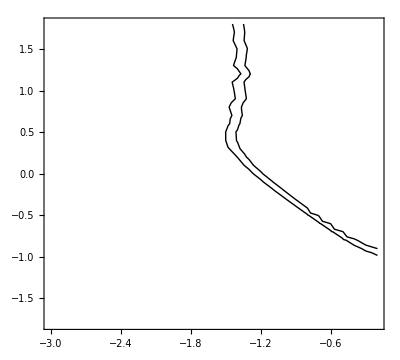

```mathematica
MyData=Import["0-code/glb/e776/pedro/E776chi.dat"];
Min[MyData⟦All,3⟧]
ListContourPlot[{Log10[#⟦1⟧],Log10[#⟦2⟧],#⟦3⟧}&/@MyData,Contours->%+MyContours,PlotRange->Full,ContourShading->False,ContourStyle->Black]

MyData=Cases[Import["3-3p1/dm41th14th24-e776-test.dat.gz"],{Repeated[_?NumericQ]}];
Min[MyData⟦All,3⟧]
ListContourPlot[{#⟦1⟧,#⟦2⟧,#⟦3⟧}&/@MyData,Contours->%+MyContours,PlotRange->Full,ContourShading->False,ContourStyle->Black]
```

#### Global fits

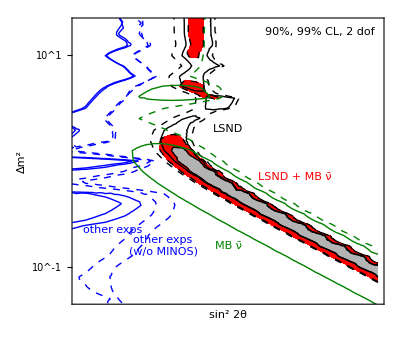

```mathematica
MyCombinedPlot=Show[MyPlot[4],MyPlot[5],MyPlot[6],MyPlot[1],MyPlot[3],PlotRange->{{-3.5,-0.5},{-1.3,1.3}},FrameLabel->{"sin^2 2θ","Δm^2"},FrameTicks->{LogTicks[-10,10],LogTicks[-5,5],LogTicksNoLabel[-10,10],LogTicksNoLabel[-5,5]},
Epilog->{
MyStyles⟦1,1⟧,Text["LSND",{-2,0.3}],
MyStyles⟦3,1⟧,Text["MB ν̄",{-2,-0.8}],
MyStyles⟦6,1⟧,Text[Style["other exps\n(w/o MINOS)",LineSpacing->{0.8,0}],{-2.65,-0.8},{0,0},{1,0.9}],
MyStyles⟦5,1⟧,Text["other exps",{-3.15,-0.65},{0,0},{1,0.9}],
Red,Text["LSND + MB ν̄",{-1.7,-0.2},{-1,-1}],
Black,Text["90%, 99% CL, 2 dof",Scaled[{0.97,0.97}],{1,1}](*,
Text[Style[Grid[{{"no evid = ","KARMEN, NOMAD, CDHS,"},{"","MBν475, Atm, Reactors, MINOS"}},Alignment->Left,Spacings->0,Background->GrayLevel[1,.7]],FontSize->14],Scaled[{0.7,0.07}]]*)
},DisplayFunction->JHEPPlot]
If[SaveFigures,
Export["fig/3p1.eps",MyCombinedPlot];
];
```

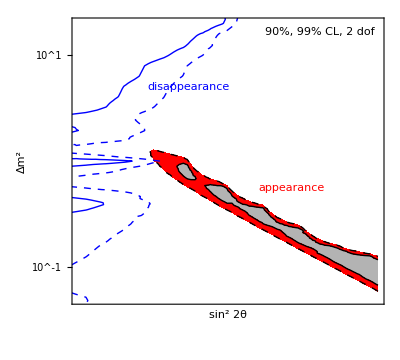

```mathematica
MyCombinedPlot=Show[MyPlot[7],MyPlot[8],PlotRange->{{-3.5,-0.5},{-1.3,1.3}},FrameLabel->{"sin^2 2θ","Δm^2"},FrameTicks->{LogTicks[-10,10],LogTicks[-5,5],LogTicksNoLabel[-10,10],LogTicksNoLabel[-5,5]},
Epilog->{
MyStyles⟦8,1⟧,Text["disappearance",{-2.4,0.7},{0,0},{1,1}],
Red,Text["appearance",{-1.7,-0.3},{-1,-1},{1,-0.5}],
Black,Text["90%, 99% CL, 2 dof",Scaled[{0.97,0.97}],{1,1}],
},DisplayFunction->JHEPPlot]
If[SaveFigures,
Export["fig/3p1-appdisapp.eps",MyCombinedPlot];
];
```

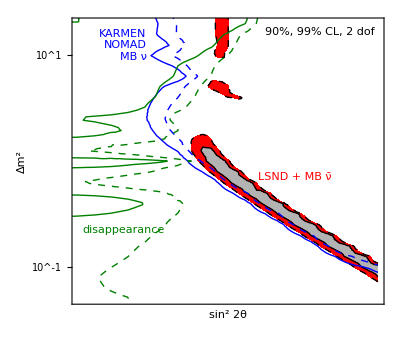

```mathematica
MyCombinedPlot=Show[MyPlot[4],MyPlot[9],MyPlot[10],PlotRange->{{-4,-0.5},{-1.3,1.3}},FrameLabel->{"sin^2 2θ","Δm^2"},FrameTicks->{LogTicks[-10,10],LogTicks[-5,5],LogTicksNoLabel[-10,10],LogTicksNoLabel[-5,5]},
Epilog->{
MyStyles⟦9,1⟧,Text[Style["KARMEN\nNOMAD\nMB ν",TextAlignment->Right],{-3.2,1.25},{1,1}],
MyStyles⟦10,1⟧,Text["disappearance",{-3.95,-0.7},{-1,-1}],
Red,Text["LSND + MB ν̄",{-1.9,-0.2},{-1,-1}],
Black,Text["90%, 99% CL, 2 dof",Scaled[{0.97,0.97}],{1,1}],
},DisplayFunction->JHEPPlot]
If[SaveFigures,
Export["fig/3p1-2.eps",MyCombinedPlot];
];
```

```mathematica
MyData=Cases[Import["results/chi2table_3p1_Um4sqDm41.dat","Table"],{Repeated[_?NumericQ]}];
MyDataInterpol=Interpolation[MyData,InterpolationOrder->1];
Chi2Min=Min[MyData⟦All,3⟧]
```

Import::nffil: File not found during Import.

Interpolation::innd: First argument in {} does not contain a list of data and coordinates.

∞

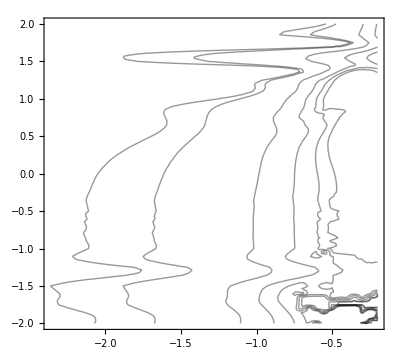

```mathematica
ContourPlot[MyDataInterpol[logUm4sq,logdm],{logUm4sq,-4,-0.2},{logdm,-2,2},Contours->Chi2Min+{χ2[2,0.1],χ2[2,0.05],20,40,60,80},ContourShading->False]
```

### Disappearance experiments

```mathematica
DataFiles="3-3p1/dm41th14th24-"<>#<>".dat.gz"&/@{"sbl","karmen-c12","karmen-c12-JR","lsnd-c12","c12"};
(*DataFiles={"3-3p1/reactor-test.dat.gz"};*)
(*DataFiles={"7-3flavor/solar-test.dat.gz"};*)
ThetaEffEE[th14_]:=Sin[2th14]^2;
For[i=1,i≤Length[DataFiles],i++,
Data[i]=Cases[Import[DataFiles⟦i⟧,"Table"],{Repeated[_?NumericQ]}];
Data[i]=Split[Sort[Data[i]],#1⟦{1,2}⟧==#2⟦{1,2}⟧&];
Data[i]={#⟦1,1⟧,Log10[ThetaEffEE[10^#⟦1,2⟧]],Min[#⟦All,-1⟧]}&/@Data[i];
DataInterpol[i]=Interpolation[Data[i],InterpolationOrder->1];
Chi2Min[i]=Min[Data[i]⟦All,-1⟧];
logdmsqMin[i]=Min[Data[i]⟦All,1⟧];
logdmsqMax[i]=Max[Data[i]⟦All,1⟧];
logthMin[i]=Min[Data[i]⟦All,2⟧];
logthMax[i]=Max[Data[i]⟦All,2⟧];
];
```

```mathematica
MyStyles={Directive[Thick,Red],Directive[Thick,Red,Dashed],Directive[Thick,Red,Dotted]};
MyContours={χ2[2,0.1],χ2[2,0.05],χ2[2,0.01]};
For[i=1,i≤Length[DataFiles],i++,
MyPlotLog[i]=
ContourPlot[DataInterpol[i][logdmsq,logth]-Chi2Min[i],{logth,logthMin[i],logthMax[i]},{logdmsq,logdmsqMin[i],logdmsqMax[i]},Contours->MyContours,ContourShading->False,ContourStyle->MyStyles,PlotRange->{{-3.5,-0.5},{-2,2},All},FrameLabel->{"sin^2 2θ","Δm^2"},FrameTicks->{LogTicks[-10,10],LogTicks[-5,5],LogTicksNoLabel[-10,10],LogTicksNoLabel[-5,5]},DisplayFunction->JHEPPlot,PlotPoints->50];
MyPlotLinear[i]=ContourPlot[DataInterpol[i][logdmsq,Log10[th]]-Chi2Min[i],{th,10^logthMin[i],10^logthMax[i]},{logdmsq,logdmsqMin[i],logdmsqMax[i]},Contours->MyContours,ContourShading->False,ContourStyle->MyStyles,PlotRange->{{0,1},{-1,2},All},FrameLabel->{"sin^2 2θ","Δm^2"},FrameTicks->{Automatic,LogTicks[-5,5],Automatic,LogTicksNoLabel[-5,5]},DisplayFunction->JHEPPlot,GridLines->Automatic,PlotPoints->50];
];
```

#### Experiments with Thomas' reactor code

Load appropriate data file and run code above, then run the following

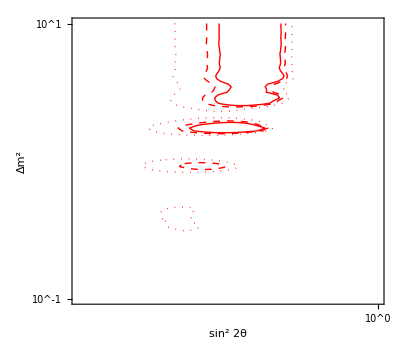

```mathematica
Show[MyPlotLog[1],FrameLabel->{"sin^2 2θ","Δm^2"},FrameTicks->{LogTicks[-10,10],LogTicks[-5,5],LogTicksNoLabel[-10,10],LogTicksNoLabel[-5,5]},PlotRange->{{-2,0},{-1,1}}]
```

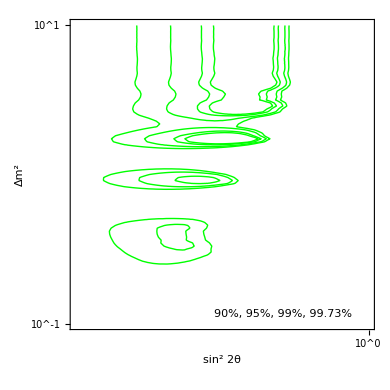

```mathematica
i=1;
MyPlot[1]=ContourPlot[DataInterpol[i][logdmsq,logth]-Chi2Min[i],{logth,logthMin[i],logthMax[i]},{logdmsq,logdmsqMin[i],logdmsqMax[i]},Contours->{χ2[2,0.1],χ2[2,0.05],χ2[2,0.01],χ2[2,0.0027]},ContourShading->False,ContourStyle->Directive[Green],PlotRange->{{-2,0},{-1,1},All},FrameLabel->{"sin^2 2θ","Δm^2"},FrameTicks->{LogTicks[-10,10],LogTicks[-5,5],LogTicksNoLabel[-10,10],LogTicksNoLabel[-5,5]},DisplayFunction->JHEPPlot,PlotPoints->50,Epilog->{Text["90%, 95%, 99%, 99.73%",Scaled[{0.7,0.05}]]},Prolog->{Inset[Import["0-code/reactors/figs/react-3p1.pdf"]⟦1⟧,Scaled[{.64,.48}]]},ImageSize->390,AspectRatio->1]
```

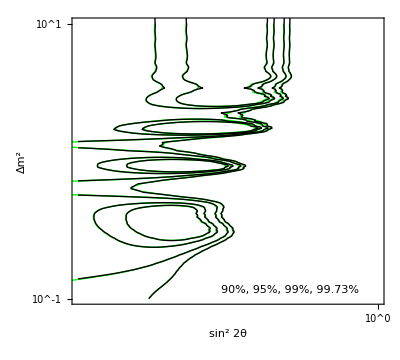

```mathematica
i=1;
MyContours={χ2[2,0.1],χ2[2,0.05],χ2[2,0.01],χ2[2,0.0027]};
ThomasData=Cases[Import["0-code/reactors/thomas/sbl_bugey.dat","Table"],{Repeated[_?NumericQ]}];
Show[
ContourPlot[DataInterpol[i][logdmsq,logth]-Chi2Min[i],{logth,logthMin[i],logthMax[i]},{logdmsq,logdmsqMin[i],logdmsqMax[i]},Contours->MyContours,ContourShading->False,ContourStyle->Directive[Green],PlotRange->{{-2,0},{-1,1},All},FrameLabel->{"sin^2 2θ","Δm^2"},FrameTicks->{LogTicks[-10,10],LogTicks[-5,5],LogTicksNoLabel[-10,10],LogTicksNoLabel[-5,5]},DisplayFunction->JHEPPlot,PlotPoints->50,Epilog->{Text["90%, 95%, 99%, 99.73%",Scaled[{0.7,0.05}]]}],
ListContourPlot[{Log10[#⟦1⟧],Log10[#⟦2⟧],#⟦3⟧}&/@ThomasData,PlotRange->All,Contours->Min[ThomasData⟦All,3⟧]+MyContours,ContourShading->False,ContourStyle->Black]
]
```

#### Experiments with Michele's solar neutrino code

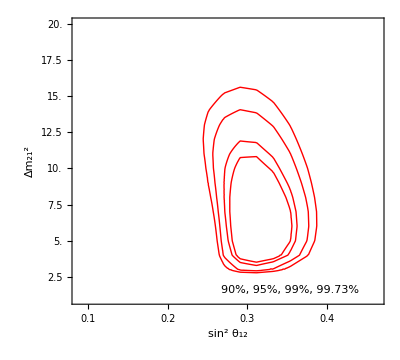

```mathematica
DataFiles={"7-3flavor/solar.dat.gz"};
For[i=1,i≤Length[DataFiles],i++,
Data[i]={Sin[#⟦1⟧]^2,#⟦2⟧,Min[#⟦3⟧,#⟦4⟧]}&/@Cases[Import[DataFiles⟦i⟧,"Table"],{Repeated[_?NumericQ]}];
DataInterpol[i]=Interpolation[Data[i],InterpolationOrder->1];
Chi2Min[i]=Min[Data[i]⟦All,-1⟧];
dmsqMin[i]=Min[Data[i]⟦All,2⟧];
dmsqMax[i]=Max[Data[i]⟦All,2⟧];
sthMin[i]=Min[Data[i]⟦All,1⟧];
sthMax[i]=Max[Data[i]⟦All,1⟧];
];
i=1;
MyPlot[1]=ContourPlot[DataInterpol[i][sth,dmsq*1*^-5]-Chi2Min[i],{sth,sthMin[i],sthMax[i]},{dmsq,dmsqMin[i]/1*^-5,dmsqMax[i]/1*^-5},Contours->{χ2[2,0.1],χ2[2,0.05],χ2[2,0.01],χ2[2,0.0027]},ContourShading->False,ContourStyle->Directive[Red,Thick],PlotRange->Full,FrameLabel->{"sin^2 θ_12","Δm_21^2"},DisplayFunction->JHEPPlot,PlotPoints->50,Epilog->{Text["90%, 95%, 99%, 99.73%",Scaled[{0.7,0.05}]]}]
```

#### Experiments with Pedro’s SBL codes

Load appropriate data file and run code above, then run the following

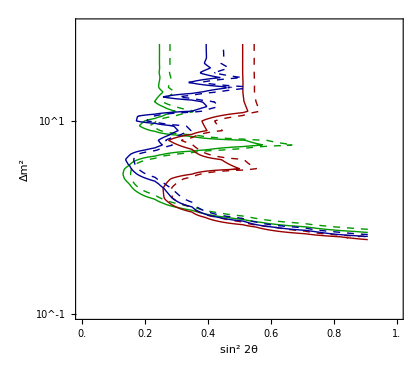

```mathematica
i=2;
j=4;
k=5;
MyStyles={Directive[Thick,RGBColor[0,.6,0]],Directive[Thick,RGBColor[0,.6,0],Dashed],Directive[Thick,RGBColor[0,.6,0],Dotted]};
MyContours={χ2[2,0.1],χ2[2,0.05]};
Show[
ContourPlot[DataInterpol[i][logdmsq,Log10[th]]-Chi2Min[i],{th,10^logthMin[i],10^logthMax[i]},{logdmsq,logdmsqMin[i],logdmsqMax[i]},Contours->MyContours,ContourShading->False,ContourStyle->MyStyles,PlotRange->{{0,1},{-1,2},All},PlotPoints->50],
ContourPlot[DataInterpol[j][logdmsq,Log10[th]]-Chi2Min[j],{th,10^logthMin[j],10^logthMax[j]},{logdmsq,logdmsqMin[j],logdmsqMax[j]},Contours->MyContours,ContourShading->False,ContourStyle->(MyStyles/.RGBColor[___]:>RGBColor[0.6,0,0]),PlotRange->{{0,1},{-1,2},All},PlotPoints->50],
ContourPlot[DataInterpol[k][logdmsq,Log10[th]]-Chi2Min[k],{th,10^logthMin[k],10^logthMax[k]},{logdmsq,logdmsqMin[k],logdmsqMax[k]},Contours->MyContours,ContourShading->False,ContourStyle->(MyStyles/.RGBColor[___]:>RGBColor[0,0,0.6]),PlotRange->{{0,1},{-1,2},All},PlotPoints->50],
Prolog->{Inset[Import["0-code/glb/c12/data/nue-carbon-analysis.pdf"]⟦1⟧,Scaled[{.44,.48}]]},
FrameLabel->{"sin^2 2θ","Δm^2"},FrameTicks->{Automatic,LogTicks[-5,5],Automatic,LogTicksNoLabel[-5,5]},DisplayFunction->JHEPPlot,ImageSize->420,AspectRatio->0.9]
```

0.551275

3.81441

34.1748

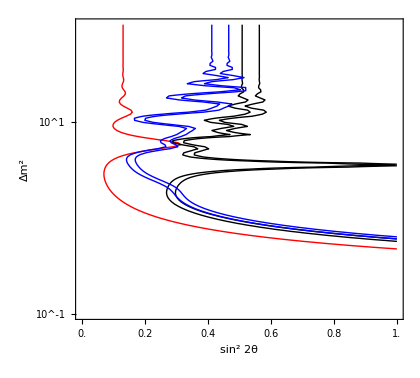

```mathematica
(* KARMEN - reproducing JR's analysis with Pedro's code, + LSND + Combi *)
Clear[MyData];
MyData[1]=Import["0-code/glb/c12/pedro-separate/KM-chi.dat"];
MyData[2]=Import["0-code/glb/c12/pedro-separate/LS-chi.dat"];
MyData[3]=Import["0-code/glb/c12/pedro-combined/comb-chi.dat"];
Min[MyData[1]⟦All,3⟧]
Min[MyData[2]⟦All,3⟧]
Min[MyData[3]⟦All,3⟧]
Show[
ListContourPlot[{#⟦2⟧,Log10[#⟦1⟧],#⟦3⟧}&/@MyData[1],Contours->{1.28},PlotRange->Full,ContourShading->False,ContourStyle->Red],
ListContourPlot[{#⟦2⟧,Log10[#⟦1⟧],#⟦3⟧}&/@MyData[2],Contours->Min[MyData[2]⟦All,3⟧]+MyContours,PlotRange->Full,ContourShading->False,ContourStyle->Black],
ListContourPlot[{#⟦1⟧,Log10[#⟦2⟧],#⟦3⟧}&/@MyData[3],Contours->Min[MyData[3]⟦All,3⟧]+MyContours,PlotRange->Full,ContourShading->False,ContourStyle->Blue],
FrameLabel->{"sin^2 2θ","Δm^2"},FrameTicks->{Automatic,LogTicks[-5,5],Automatic,LogTicksNoLabel[-5,5]},DisplayFunction->JHEPPlot,Prolog->{Inset[Import["0-code/glb/c12/data/preliminary-karmen-nue-carbon-JR.pdf"]⟦1⟧,Scaled[{.44,.48}]]},ImageSize->420,AspectRatio->0.9]
```

0.303905

3.81466

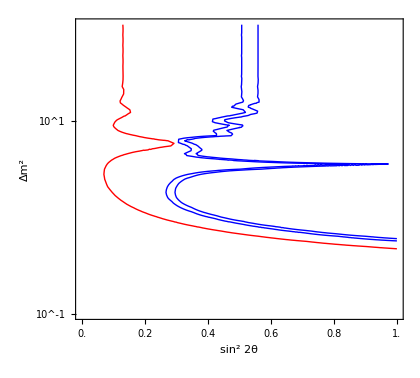

```mathematica
(* KARMEN - reproducing JR's analysis with a 2 flavor fit *)
Clear[MyData];
DataFiles="3-3p1/"<>#<>".dat.gz"&/@{"karmen-c12-2flavor-JR","lsnd-c12-2flavor"};
For[i=1,i≤Length[DataFiles],i++,
MyData[i]=Cases[Import[DataFiles⟦i⟧],{Repeated[_?NumericQ]}];
MyData[i]={Sin[2 10^#⟦2⟧]^2,#⟦1⟧,Min[#⟦3⟧,#⟦4⟧]}&/@MyData[i];
MyDataInterpol[i]=Interpolation[MyData[i],InterpolationOrder->1];
];
Min[MyData[1]⟦All,3⟧]
Min[MyData[2]⟦All,3⟧]
Show[
ContourPlot[MyDataInterpol[1][s22th,logdm],{s22th,0,1},{logdm,-1,2},Contours->{χ2[1,0.2]},PlotRange->Full,ContourShading->False,ContourStyle->Red],
ContourPlot[MyDataInterpol[2][s22th,logdm],{s22th,0,1},{logdm,-1,2},Contours->Min[MyData[2]⟦All,3⟧]+MyContours,PlotRange->Full,ContourShading->False,ContourStyle->Blue],
FrameLabel->{"sin^2 2θ","Δm^2"},FrameTicks->{Automatic,LogTicks[-5,5],Automatic,LogTicksNoLabel[-5,5]},DisplayFunction->JHEPPlot,Prolog->{Inset[Import["0-code/glb/c12/data/preliminary-karmen-nue-carbon-JR.pdf"]⟦1⟧,Scaled[{.44,.48}]]},ImageSize->420,AspectRatio->0.9]
```

### More Global fits

#### θ_24 vs. θ_34

```mathematica
DataFiles="3-3p1/"<>#&/@{"th24th34-all.dat.gz","th24th34-evid.dat.gz","th24th34-noevid.dat.gz"};
For[i=1,i≤Length[DataFiles],i++,
Data[i]=Data[i]=Cases[Import[DataFiles⟦i⟧,"Table"],{Repeated[_?NumericQ]}];
Data[i]={#⟦1,1⟧,#⟦1,2⟧,Min[#⟦All,{-2,-1}⟧]}&/@Split[Data[i],#1⟦1;;2⟧==#2⟦1;;2⟧&];
DataInterpol[i]=Interpolation[Data[i],InterpolationOrder->1];

th24Min[i]=Min[Data[i]⟦All,1⟧];
th24Max[i]=Max[Data[i]⟦All,1⟧];
th34Min[i]=Min[Data[i]⟦All,2⟧];
th34Max[i]=Max[Data[i]⟦All,2⟧];

BFPoint[i]=Sort[Data[i],OrderedQ[{#1⟦-1⟧,#2⟦-1⟧}]&]⟦1⟧;
{Chi2Min[i],BFPoint[i]}=FindMinimum[DataInterpol[i][th24,th34],{th24,BFPoint[i]⟦1⟧,th24Min[i],th24Max[i]},{th34,BFPoint[i]⟦2⟧,th34Min[i],th34Max[i]}]/.Rule[s_,x_]:>x;
];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than TraditionalForm`MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::reged: The point TraditionalForm`{0.0001, 0.0500929} is at the edge of the search region TraditionalForm`{0.0001, 0.45} in coordinate TraditionalForm`1 and the computed search direction points outside the region.

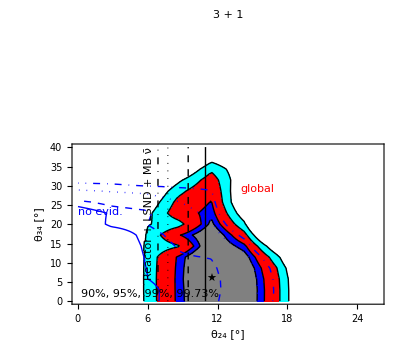

```mathematica
MyContours={χ2[2,0.1],χ2[2,0.05],χ2[2,0.01],χ2[2,PValue[3]]};
MyOptions={{ContourShading->{Gray,Blue,Red,Cyan,None},ContourStyle->Black},
{ContourShading->None,ContourStyle->(Directive[Thick,Black,#]&/@{Dashing[{}],Dashed,Dotted,DotDashed})},
{ContourShading->None,ContourStyle->(Directive[Thick,Blue,#]&/@{Dashing[{}],Dashed,Dotted,DotDashed})}};
For[i=1,i≤Length[DataFiles],i++,
MyPlot[i]=ContourPlot[DataInterpol[i][th24 Degree,th34 Degree]-Chi2Min[i],{th24,th24Min[i]/Degree,th24Max[i]/Degree},{th34,th34Min[i]/Degree,th34Max[i]/Degree},Contours->MyContours,PlotRange->Full,Evaluate[Sequence@@MyOptions⟦i⟧]]
];
MyCombinedPlot[1]=Show[MyPlot[1],MyPlot[2],MyPlot[3],
FrameLabel->{"θ_24 [°]","θ_34 [°]"},PlotLabel->"3 + 1",
Epilog->{
Text["90%, 95%, 99%, 99.73%",Scaled[{0.03,0.03}],{-1,-1}],Text["★",BFPoint[1]/Degree],
Black,Text["Reactor + LSND + MB ν̄",{6.5,40},{1,-1},{0,1},Background->GrayLevel[1,0.5]],
Red,Text["global",{14,28},{-1,-1},{0.2,-1}],
Blue,Text["no evid.",{0,22},{-1,-1},{0.4,-1}]
}]
If[SaveFigures,
Export["fig/global-fit-3p2.eps",MyCombinedPlot[1]];
];
```

#### θ_24 vs. θ_34 vs. Δm_41^2

```mathematica
DataFiles="3-3p1/"<>#&/@{"th24th34dm41-noevid.dat.gz","th24th34dm41-minos.dat.gz"};
For[i=1,i≤Length[DataFiles],i++,
Data[i]=Data[i]=Cases[Import[DataFiles⟦i⟧,"Table"],{Repeated[_?NumericQ]}];
Data[i]={Log10[Sin[#⟦1⟧]^2],Log10[Sin[#⟦2⟧]^2],#⟦3⟧,Min[#⟦{-2,-1}⟧]}&/@Data[i];
DataInterpol[i]=Interpolation[Data[i],InterpolationOrder->1];
Data12[i]={#⟦1,1⟧,#⟦1,2⟧,Min[#⟦All,-1⟧]}&/@Gather[Data[i],#1⟦{1,2}⟧==#2⟦{1,2}⟧&];
DataInterpol12[i]=Interpolation[Data12[i],InterpolationOrder->1];
Data13[i]={#⟦1,1⟧,#⟦1,3⟧,Min[#⟦All,-1⟧]}&/@Gather[Data[i],#1⟦{1,3}⟧==#2⟦{1,3}⟧&];
DataInterpol13[i]=Interpolation[Data13[i],InterpolationOrder->1];
Data32[i]={#⟦1,3⟧,#⟦1,2⟧,Min[#⟦All,-1⟧]}&/@Gather[Data[i],#1⟦{3,2}⟧==#2⟦{3,2}⟧&];
DataInterpol32[i]=Interpolation[Data32[i],InterpolationOrder->1];

th24Min[i]=Min[Data[i]⟦All,1⟧];
th24Max[i]=Max[Data[i]⟦All,1⟧];
th34Min[i]=Min[Data[i]⟦All,2⟧];
th34Max[i]=Max[Data[i]⟦All,2⟧];
dm41Min[i]=Min[Data[i]⟦All,3⟧];
dm41Max[i]=Max[Data[i]⟦All,3⟧];

BFPoint[i]=Sort[Data[i],OrderedQ[{#1⟦-1⟧,#2⟦-1⟧}]&]⟦1⟧;
{Chi2Min[i],BFPoint[i]}=FindMinimum[DataInterpol[i][th24,th34,dm41],{th24,BFPoint[i]⟦1⟧,th24Min[i],th24Max[i]},{th34,BFPoint[i]⟦2⟧,th34Min[i],th34Max[i]},{dm41,BFPoint[i]⟦3⟧,dm41Min[i],dm41Max[i]}]/.Rule[s_,x_]:>x;

th24Min[i]=th34Min[i]=-3;
dm41Min[i]=-1.7;
dm41Max[i]=1.7;
];
```

FindMinimum::reged: The point TraditionalForm`{-1.59507, -8., 1.4} is at the edge of the search region TraditionalForm`{-8., -0.381935} in coordinate TraditionalForm`2 and the computed search direction points outside the region.

FindMinimum::reged: The point TraditionalForm`{-1.1169, -8., 1.3} is at the edge of the search region TraditionalForm`{-8., -0.381935} in coordinate TraditionalForm`2 and the computed search direction points outside the region.

```mathematica
MyContours={χ2[2,0.1],χ2[2,0.05],χ2[2,0.01],χ2[2,PValue[3]]};
MyOptions={{ContourShading->{GrayLevel[0.8],Blue,Red,Cyan,None},ContourStyle->Black},
{ContourShading->None,ContourStyle->(Directive[Thick,Black,#]&/@{Dashing[{}],Dashed,Dotted,DotDashed})}};
For[i=1,i≤Length[DataFiles],i++,
MyPlot12[i]=ContourPlot[DataInterpol12[i][th24,th34]-Chi2Min[i],{th24,th24Min[i],th24Max[i]},{th34,th34Min[i],th34Max[i]},Contours->MyContours,PlotRange->Full,Evaluate[Sequence@@MyOptions⟦i⟧]];
MyPlot13[i]=ContourPlot[DataInterpol13[i][th24,dm41]-Chi2Min[i],{th24,th24Min[i],th24Max[i]},{dm41,dm41Min[i],dm41Max[i]},Contours->MyContours,PlotRange->Full,Evaluate[Sequence@@MyOptions⟦i⟧]];
MyPlot32[i]=ContourPlot[DataInterpol32[i][dm41,th34]-Chi2Min[i],{dm41,dm41Min[i],dm41Max[i]},{th34,th34Min[i],th34Max[i]},Contours->MyContours,PlotRange->Full,Evaluate[Sequence@@MyOptions⟦i⟧]];
];
```

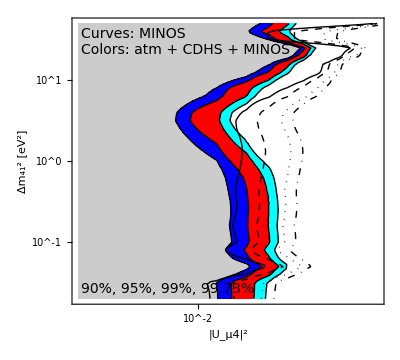
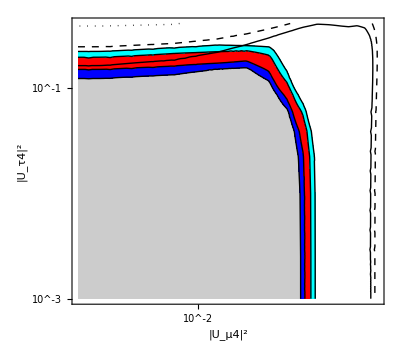
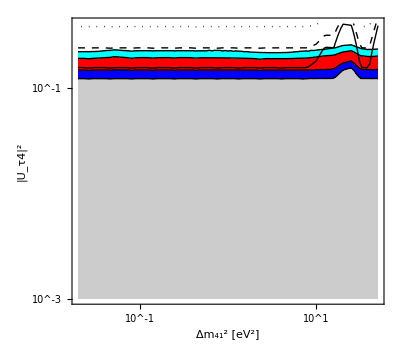
-Graphics- | 
-Graphics- | -Graphics-

```mathematica
i=99;
MyPlot12[i]=Show[MyPlot12[1],MyPlot12[2],FrameLabel->{"|U_μ4|^2","|U_τ4|^2"},FrameTicks->{LogTicks[-5,5],LogTicks[-5,5],LogTicksNoLabel[-5,5],LogTicksNoLabel[-5,5]},Epilog->{}];
MyPlot13[i]=Show[MyPlot13[1],MyPlot13[2],FrameLabel->{"|U_μ4|^2","Δm_41^2 [eV^2]"},FrameTicks->{LogTicks[-5,5],LogTicks[-3,3],LogTicksNoLabel[-5,5],LogTicksNoLabel[-3,3]},Epilog->{Text[Style["90%, 95%, 99%, 99.73%",FontSize->14],Scaled[{0.03,0.03}],{-1,-1}],Text[Style["Curves: MINOS\nColors: atm + CDHS + MINOS",TextAlignment->Left,FontSize->14],Scaled[{0.03,0.97}],{-1,1}]}];
MyPlot32[i]=Show[MyPlot32[1],MyPlot32[2],FrameLabel->{"Δm_41^2 [eV^2]","|U_τ4|^2"},FrameTicks->{LogTicks[-3,3],LogTicks[-5,5],LogTicksNoLabel[-3,3],LogTicksNoLabel[-5,5]},Epilog->{}];
Grid[{{MyPlot13[i],Null},{MyPlot12[i],MyPlot32[i]}}]
If[SaveFigures,
Export["fig/th24th34dm41-minos.eps",%];
];
```

#### θ_23 vs. θ_13 vs. Δm_31^2

```mathematica
DataFiles="2-smparams/"<>#&/@{"th23dm31-5f-all.dat.gz","th13dm31-5f-all.dat.gz","th23th13-5f-all.dat.gz",
"th23dm31-3f-all.dat.gz","th13dm31-3f-all.dat.gz","th23th13-3f-all.dat.gz"};
For[i=1,i≤Length[DataFiles],i++,
Data[i]=Data[i]=Cases[Import[DataFiles⟦i⟧,"Table"],{Repeated[_?NumericQ]}];
Data[i]={#⟦1,1⟧,#⟦1,2⟧,Min[#⟦All,{-2,-1}⟧]}&/@Gather[Data[i],#1⟦{1,2}⟧==#2⟦{1,2}⟧&];
Data[i]=Switch[Mod[i,3],
1,{Sin[#⟦1⟧]^2,#⟦2⟧,#⟦3⟧}&/@Data[i],
2,{Sin[2*10^#⟦1⟧]^2,#⟦2⟧,#⟦3⟧}&/@Data[i],
0,{Sin[#⟦1⟧]^2,Sin[2*10^#⟦2⟧]^2,#⟦3⟧}&/@Data[i]
];
DataInterpol[i]=Interpolation[Data[i],InterpolationOrder->1];

p1Min[i]=Min[Data[i]⟦All,1⟧];
p1Max[i]=Max[Data[i]⟦All,1⟧];
p2Min[i]=Min[Data[i]⟦All,2⟧];
p2Max[i]=Max[Data[i]⟦All,2⟧];

BFPoint[i]=Sort[Data[i],OrderedQ[{#1⟦-1⟧,#2⟦-1⟧}]&]⟦1⟧;
{Chi2Min[i],BFPoint[i]}=FindMinimum[DataInterpol[i][p1,p2],{p1,BFPoint[i]⟦1⟧,p1Min[i],p1Max[i]},{p2,BFPoint[i]⟦2⟧,p2Min[i],p2Max[i]}]/.Rule[s_,x_]:>x;
];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than TraditionalForm`MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum :: lstol will be suppressed during this calculation.

```mathematica
MyContours={χ2[2,0.1],χ2[2,0.05],χ2[2,0.01],χ2[2,PValue[3]]};
MyOptions={{ContourShading->(Lighter[#]&/@{Gray,Blue,Red,Cyan,White}),ContourStyle->None},{ContourShading->None,ContourStyle->(Directive[Thick,Black,#]&/@{Dashing[{}],Dashed,Dotted,DotDashed})}};
MyFrameLabels={{"Sin^2 θ_23","Δm_31^2 [eV^2]"},{"Sin^2 2θ_13","Δm_31^2 [eV^2]"},{"Sin^2 θ_23","Sin^2 2θ_13"}};
For[i=1,i≤Length[DataFiles],i++,
MyPlot[i]=ContourPlot[DataInterpol[i][p1,p2]-Chi2Min[i],{p1,p1Min[i],p1Max[i]},{p2,p2Min[i],p2Max[i]},Contours->MyContours,PlotRange->Full,Evaluate[Sequence@@MyOptions⟦Floor[(i-1)/3]+1⟧],FrameLabel->MyFrameLabels⟦Mod[i-1,3]+1⟧,ImagePadding->{{100,20},{50,20}}];
];
```

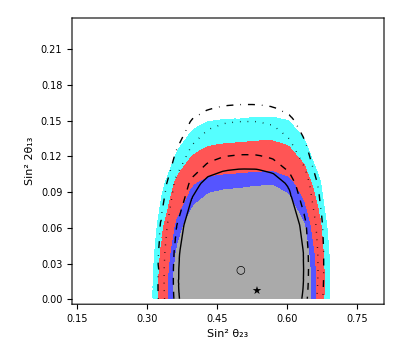
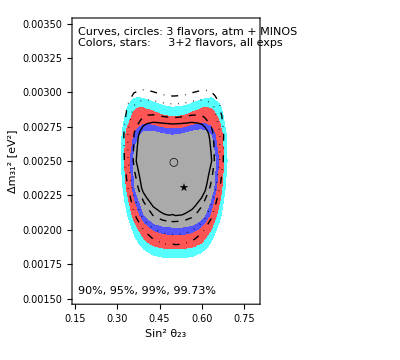
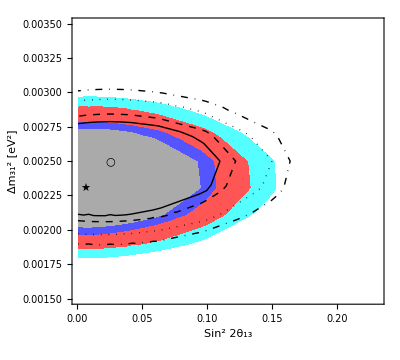
-Graphics- | 
-Graphics- | -Graphics-

```mathematica
Grid[{{
Show[MyPlot[3],MyPlot[6],PlotRange->All,Epilog->{Text["★",BFPoint[3]],Text["○",BFPoint[6]]}],Null},
{Show[MyPlot[1],MyPlot[4],PlotRange->All,Epilog->{
Text["★",BFPoint[1]],Text["○",BFPoint[4]],
Text["90%, 95%, 99%, 99.73%",Scaled[{0.03,0.03}],{-1,-1}],Text[Style["Curves, circles: 3 flavors, atm + MINOS\nColors, stars:     3+2 flavors, all exps",TextAlignment->Left],Scaled[{0.03,0.97}],{-1,1}]}],
Show[MyPlot[2],MyPlot[5],PlotRange->All,Epilog->{Text["★",BFPoint[2]],Text["○",BFPoint[5]]}]}}]
If[SaveFigures,
Export["fig/th23dm31th13.eps",%];
];
```

#### Δm_41^2 vs. Δm_51^2

```mathematica
DataFiles={"4-3p2/dm41dm51-all.dat.gz","5-1p3p1/dm41dm51-all.dat.gz"};
For[i=1,i≤Length[DataFiles],i++,
Data[i]=Cases[Import[DataFiles⟦i⟧],{Repeated[_Real|_Integer]}];
Data[i]={#⟦1⟧,#⟦2⟧,Min[#⟦3⟧,#⟦4⟧]}&/@Data[i];
DataInterpol[i]=Interpolation[Data[i],InterpolationOrder->3];
Chi2Min[i]=Min[Data[i]⟦All,-1⟧];
BFPoint[i]=Select[Data[i],#⟦-1⟧==Chi2Min[i]&]⟦1,1;;2⟧;
Print["χ_min^2 = ",Chi2Min[i],", best fit: ",BFPoint[i]];
];
```

χ_min^2 = 245.332, best fit: {-0.325,-0.05}

χ_min^2 = 241.78, best fit: {-0.325,-0.05}

```mathematica
BFPoint[1]=Log10[{0.82,1.1}]
BFPoint[2]=Log10[{0.48,0.9}]
```

{-0.0861861,0.0413927}

{-0.318759,-0.0457575}

```mathematica
MyContours={χ2[2,0.1],χ2[2,0.05],χ2[2,0.01],χ2[2,PValue[3]]};
For[i=1,i≤Length[DataFiles],i++,
MyPlot[i]=ContourPlot[DataInterpol[i][logdm41,logdm51]-Chi2Min[i],{logdm41,-1,1},{logdm51,-1,1},PlotRange->Full,Contours->MyContours,PlotRange->All,ContourShading->{Gray,Blue,Red,Cyan,None},ContourStyle->Black,FrameTicks->{LogTicks[-5,5],LogTicks[-5,5],LogTicksNoLabel[-5,5],LogTicksNoLabel[-5,5]},FrameLabel->{"Δm_41 [eV^2]","Δm_51 [eV^2]"},(*PlotLabel->"SBL + Atm + MINOS",*)RegionFunction->If[StringCases[DataFiles⟦i⟧,"1p3p1"]≠{},(#1>#2&),(#2≥#1&)]];
];
```

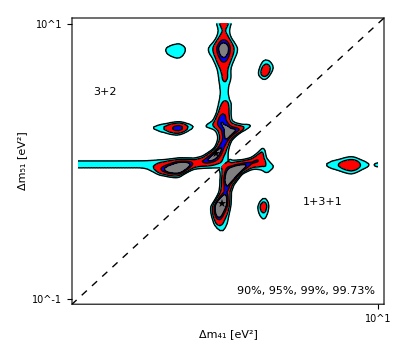

```mathematica
MyCombiPlot=Show[MyPlot[1],MyPlot[2],
Epilog->{
Dashed,Line[{{-5,-5},{5,5}}],
Text["90%, 95%, 99%, 99.73%",Scaled[{0.97,0.03}],{1,-1}],
Text["3+2",{-0.9,0.5},{-1,0}],Text["1+3+1",{0.5,-0.3},{-1,0}],
Text["★",Sort[BFPoint[1]]],Text["★",Sort[BFPoint[2],Greater]]
}]
If[SaveFigures,
Export["fig/dm41dm51.eps",MyCombiPlot];
];
```

### Parameter goodness of fit test

```mathematica
n=3;
U3=RotationMatrix[-"TH23",{UnitVector[n,2],UnitVector[n,3]}].
DiagonalMatrix[{Exp[-I "DELTA_0"],1,1}].RotationMatrix[-"TH13",{UnitVector[n,1],UnitVector[n,3]}].DiagonalMatrix[{Exp[I "DELTA_0"],1,1}].
RotationMatrix[-"TH12",{UnitVector[n,1],UnitVector[n,2]}];

n=4;
U4=RotationMatrix[-"TH34",{UnitVector[n,3],UnitVector[n,4]}].
DiagonalMatrix[{1,1,1,Exp[-I "DELTA_1"]}].RotationMatrix[-"TH24",{UnitVector[n,2],UnitVector[n,4]}].DiagonalMatrix[{1,1,1,Exp[I "DELTA_1"]}].
RotationMatrix[-"TH14",{UnitVector[n,1],UnitVector[n,4]}].
RotationMatrix[-"TH23",{UnitVector[n,2],UnitVector[n,3]}].
DiagonalMatrix[{1,1,Exp[-I "DELTA_0"],1}].RotationMatrix[-"TH13",{UnitVector[n,1],UnitVector[n,3]}].DiagonalMatrix[{1,1,Exp[I "DELTA_0"],1}].
DiagonalMatrix[{1,Exp[-I "DELTA_2"],1,1}].RotationMatrix[-"TH12",{UnitVector[n,1],UnitVector[n,2]}].DiagonalMatrix[{1,Exp[I "DELTA_2"],1,1}];

n=5;
U5=RotationMatrix[-"TH45",{UnitVector[n,4],UnitVector[n,5]}].
RotationMatrix[-"TH35",{UnitVector[n,3],UnitVector[n,5]}].
RotationMatrix[-"TH25",{UnitVector[n,2],UnitVector[n,5]}].
DiagonalMatrix[{1,1,1,1,Exp[-I "DELTA_2"]}].RotationMatrix[-"TH15",{UnitVector[n,1],UnitVector[n,5]}].DiagonalMatrix[{1,1,1,1,Exp[I "DELTA_2"]}].
RotationMatrix[-"TH34",{UnitVector[n,3],UnitVector[n,4]}].
RotationMatrix[-"TH24",{UnitVector[n,2],UnitVector[n,4]}].
DiagonalMatrix[{1,1,1,Exp[-I "DELTA_1"],1}].RotationMatrix[-"TH14",{UnitVector[n,1],UnitVector[n,4]}].DiagonalMatrix[{1,1,1,Exp[I "DELTA_1"],1}].
RotationMatrix[-"TH23",{UnitVector[n,2],UnitVector[n,3]}].
DiagonalMatrix[{1,1,Exp[-I "DELTA_0"],1,1}].RotationMatrix[-"TH13",{UnitVector[n,1],UnitVector[n,3]}].DiagonalMatrix[{1,1,Exp[I "DELTA_0"],1,1}].
RotationMatrix[-"TH12",{UnitVector[n,1],UnitVector[n,2]}];

n=3;
DataFiles="7-3flavor/pg/"<>#&/@{
"all-atmtab-old.dat.gz","disapp-atmtab-old.dat.gz","app-old.dat.gz","noevid-atmtab-old.dat.gz","evid-old.dat.gz",
"all-atmtab-new.dat.gz","disapp-atmtab-new.dat.gz","app-new.dat.gz","noevid-atmtab-new.dat.gz","evid-new.dat.gz",
"all-atmcomp-old.dat.gz","disapp-atmcomp-old.dat.gz","noevid-atmcomp-old.dat.gz",
"all-atmcomp-new.dat.gz","disapp-atmcomp-new.dat.gz","noevid-atmcomp-new.dat.gz",
"all-old.dat.gz","disapp-old.dat.gz","noevid-old.dat.gz",
"all-new.dat.gz","disapp-new.dat.gz","noevid-new.dat.gz"(*,"noevid-app-new.dat.gz"*)};
For[i=1,i≤Length[DataFiles],i++,
MyLabel[i]=FileBaseName[DataFiles⟦i⟧];
Data[MyLabel[i]]=Data[i]=Cases[Import[DataFiles⟦i⟧,"Table"],{Repeated[_?NumericQ]}];
Chi2[MyLabel[i]]=Chi2[i]=Min[Data[MyLabel[i]]⟦All,{-2,-1}⟧];

Params[i]=Import[DataFiles⟦i⟧,"String"];
Params[i]=Flatten[ImportString[#,"Table"]]⟦2;;-1⟧&/@StringCases[Params[i],RegularExpression["(?m)"<>ToString[InputForm[Chi2[i]]]<>".*\n(.*\n.*\n.*\n.*\n)"]->"$1"];
Params[MyLabel[i]]=Params[i]=Map[#⟦1⟧->#⟦2⟧&,#,{1}]&/@(Partition[#,2]&/@Params[i]);
Switch[n,
3,UPMNS[MyLabel[i]]=UPMNS[i]=U3/.Params[i]⟦1⟧,
4,UPMNS[MyLabel[i]]=UPMNS[i]=U4/.Params[i]⟦1⟧,
5,UPMNS[MyLabel[i]]=UPMNS[i]=U5/.Params[i]⟦1⟧
];
];
```

```mathematica
Params["all-new"]
```

{{TH12→0.601264,TH13→0.0741133,TH23→0.789495,DELTA_0→5.63713,DM21→0.000076,DM31→0.00245951,DM41→3.98107,TH14→1.×10^-7,TH24→1.×10^-7,TH34→1.×10^-7,PARAMS_IH→TH12,0.601264→TH13,0.0740186→TH23,0.789201→DELTA_0}}

```mathematica
Abs[UPMNS["all-new"]]//MatrixForm
Arg[UPMNS["all-new"]⟦2,4⟧*Conjugate[UPMNS["all-new"]⟦1,4⟧*UPMNS["all-new"]⟦2,5⟧]*UPMNS["all-new"]⟦1,5⟧]/π
```

(0.822358 | 0.564132 | 0.0740455
0.433759 | 0.557243 | 0.708049
0.368214 | 0.60929 | 0.702271)

Part::partw: Part TraditionalForm`4 of TraditionalForm`{-0.432973 + 0.0260997\ ⅈ, 0.556956  + 0.0179043\ ⅈ, 0.708049}
 does not exist.

Part::partw: Part TraditionalForm`4 of TraditionalForm`{0.822358, 0.564132, 0.0591227  + 0.0445784\ ⅈ}
 does not exist.

Part::partw: Part TraditionalForm`5 of TraditionalForm`{-0.432973 + 0.0260997\ ⅈ, 0.556956  + 0.0179043\ ⅈ, 0.708049}
 does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

1/π arg((0.822358 | 0.564132 | 0.0591227+0.0445784 ⅈ
-0.432973+0.0260997 ⅈ | 0.556956+0.0179043 ⅈ | 0.708049
0.367303+0.0258868 ⅈ | -0.609031+0.0177582 ⅈ | 0.702271)⟦1,5⟧ (0.822358 | 0.564132 | 0.0591227+0.0445784 ⅈ
-0.432973+0.0260997 ⅈ | 0.556956+0.0179043 ⅈ | 0.708049
0.367303+0.0258868 ⅈ | -0.609031+0.0177582 ⅈ | 0.702271)⟦2,4⟧ Conjugate[((0.822358 | 0.564132 | 0.0591227+0.0445784 ⅈ
-0.432973+0.0260997 ⅈ | 0.556956+0.0179043 ⅈ | 0.708049
0.367303+0.0258868 ⅈ | -0.609031+0.0177582 ⅈ | 0.702271)⟦1,4⟧ (0.822358 | 0.564132 | 0.0591227+0.0445784 ⅈ
-0.432973+0.0260997 ⅈ | 0.556956+0.0179043 ⅈ | 0.708049
0.367303+0.0258868 ⅈ | -0.609031+0.0177582 ⅈ | 0.702271)⟦2,5⟧)])

```mathematica
Print["MINOS not included, atmospherics tabulated:"];
Grid[{{"","old","new"},
{"All experiments",Chi2["all-atmtab-old"],Chi2["all-atmtab-new"]},
{"Disppearance",Chi2["disapp-atmtab-old"],Chi2["disapp-atmtab-new"]},
{"Appearance",Chi2["app-old"],Chi2["app-new"]},
{"No evidence",Chi2["noevid-atmtab-old"],Chi2["noevid-atmtab-new"]},
{"Evidence (LSND+MBanti)",Chi2["evid-old"],Chi2["evid-new"]}
},Alignment->Left,Dividers->{None,{1->True,2->True,-1->True}},Spacings->{3,0.5}]
Switch[n,
3,dofTable={0,0,0,0},
4,dofTable={2,2,2,2},
5,dofTable={5,5,4,4}
];
PGTable={Chi2["all-atmtab-old"]-Chi2["noevid-atmtab-old"]-Chi2["evid-old"],
Chi2["all-atmtab-new"]-Chi2["noevid-atmtab-new"]-Chi2["evid-new"],
Chi2["all-atmtab-old"]-Chi2["disapp-atmtab-old"]-Chi2["app-old"],
Chi2["all-atmtab-new"]-Chi2["disapp-atmtab-new"]-Chi2["app-new"]};
If[n>3,Grid[{
{"","evid vs. noevid (5 dof)",SpanFromLeft,"app vs. disapp (4 dof)",SpanFromLeft},
{"","old","new","old","new"},
Flatten[{"χ^2",PGTable⟦1;;4⟧}],
Flatten[{"PG",Table[N[1-CDF[ChiSquareDistribution[dofTable⟦k⟧]][PGTable⟦k⟧]],{k,1,4}]}]
},Spacings->{3,0.5},Dividers->{None,{1->True,3->True,-1->True}}]]

Print["MINOS not included, Michele's full atmospherics code included:"];
Grid[{{"","old","new"},
{"All experiments",Chi2["all-atmcomp-old"],Chi2["all-atmcomp-new"]},
{"Disppearance",Chi2["disapp-atmcomp-old"],Chi2["disapp-atmcomp-new"]},
{"Appearance",Chi2["app-old"],Chi2["app-new"]},
{"No evidence",Chi2["noevid-atmcomp-old"],Chi2["noevid-atmcomp-new"]},
{"Evidence (LSND+MBanti)",Chi2["evid-old"],Chi2["evid-new"]}
},Alignment->Left,Dividers->{None,{1->True,2->True,-1->True}},Spacings->{3,0.5}]
PGTable={Chi2["all-atmcomp-old"]-Chi2["noevid-atmcomp-old"]-Chi2["evid-old"],
Chi2["all-atmcomp-new"]-Chi2["noevid-atmcomp-new"]-Chi2["evid-new"],
Chi2["all-atmcomp-old"]-Chi2["disapp-atmcomp-old"]-Chi2["app-old"],
Chi2["all-atmcomp-new"]-Chi2["disapp-atmcomp-new"]-Chi2["app-new"]};
If[n>3,Grid[{
{"","evid vs. noevid (5 dof)",SpanFromLeft,"app vs. disapp (4 dof)",SpanFromLeft},
{"","old","new","old","new"},
Flatten[{"χ^2",PGTable⟦1;;4⟧}],
Flatten[{"PG",Table[N[1-CDF[ChiSquareDistribution[dofTable⟦k⟧]][PGTable⟦k⟧]],{k,1,4}]}]
},Spacings->{3,0.5},Dividers->{None,{1->True,3->True,-1->True}}]]

Print["MINOS included, Michele's full atmospherics code included:"];
Grid[{{"","old","new"},
{"All experiments",Chi2["all-old"],Chi2["all-new"]},
{"Disppearance",Chi2["disapp-old"],Chi2["disapp-new"]},
{"Appearance",Chi2["app-old"],Chi2["app-new"]},
{"No evidence",Chi2["noevid-old"],Chi2["noevid-new"]},
{"Evidence (LSND+MBanti)",Chi2["evid-old"],Chi2["evid-new"]}
},Alignment->Left,Dividers->{None,{1->True,2->True,-1->True}},Spacings->{3,0.5}]
PGTable={Chi2["all-old"]-Chi2["noevid-old"]-Chi2["evid-old"],
Chi2["all-new"]-Chi2["noevid-new"]-Chi2["evid-new"],
Chi2["all-old"]-Chi2["disapp-old"]-Chi2["app-old"],
Chi2["all-new"]-Chi2["disapp-new"]-Chi2["app-new"]};
If[n>3,Grid[{
{"","evid vs. noevid (5 dof)",SpanFromLeft,"app vs. disapp (4 dof)",SpanFromLeft},
{"","old","new","old","new"},
Flatten[{"χ^2",PGTable⟦1;;4⟧}],
Flatten[{"PG",Table[N[1-CDF[ChiSquareDistribution[dofTable⟦k⟧]][PGTable⟦k⟧]],{k,1,4}]}]
},Spacings->{3,0.5},Dividers->{None,{1->True,3->True,-1->True}}]]
```

MINOS not included, atmospherics tabulated:

| old | new
All experiments | 155.607 | 156.256
Disppearance | 79.1619 | 79.8111
Appearance | 76.4453 | 76.4453
No evidence | 87.3228 | 87.972
Evidence (LSND+MBanti) | 68.2843 | 68.2843

MINOS not included, Michele's full atmospherics code included:

| old | new
All experiments | 235.442 | 236.091
Disppearance | 158.996 | 159.645
Appearance | 76.4453 | 76.4453
No evidence | 167.157 | 167.806
Evidence (LSND+MBanti) | 68.2843 | 68.2843

MINOS included, Michele's full atmospherics code included:

| old | new
All experiments | 286.984 | 287.595
Disppearance | 210.539 | 211.15
Appearance | 76.4453 | 76.4453
No evidence | 218.7 | 219.311
Evidence (LSND+MBanti) | 68.2843 | 68.2843

NOTE : Number of degrees of freedom not yet understood

```mathematica
3+2 Bugey Total Rates
```

| old | new
All experiments | 199.897 | 144.209
Disppearance | 153.601 | 104.838
Appearance | 26.3971 | 26.3966
No evidence | 161.762 | 112.999
Evidence (LSND+MBanti) | 12.9423 | 12.9423

| evid vs. noevid (5 dof) |  | app vs. disapp (4 dof) | 
 | old | new | old | new
χ^2 | 25.1924 | 18.2675 | 19.8986 | 12.9742
PG | 0.000127904 | 0.00262921 | 0.000522958 | 0.0114025

```mathematica
3+2 Standard
```

| old | new
All experiments | 199.897 | 189.002
Disppearance | 153.601 | 147.586
Appearance | 26.3971 | 26.3971
No evidence | 161.762 | 155.732
Evidence (LSND+MBanti) | 12.9423 | 12.9423

| evid vs. noevid (5 dof) |  | app vs. disapp (4 dof) | 
 | old | new | old | new
χ^2 | 25.1924 | 20.3279 | 19.8986 | 15.0186
PG | 0.000127904 | 0.00108444 | 0.000522958 | 0.00466284

```mathematica
1+3+1 Bugey Total Rates
```

| old | new
All experiments | 194.603 | 140.969
Disppearance | 153.601 | 104.838
Appearance | 26.3961 | 26.3821
No evidence | 161.762 | 113.
Evidence (LSND+MBanti) | 12.9423 | 12.9423

| evid vs. noevid (5 dof) |  | app vs. disapp (4 dof) | 
 | old | new | old | new
χ^2 | 19.8981 | 15.0275 | 14.6052 | 9.7493
PG | 0.00130596 | 0.0102453 | 0.00559408 | 0.0448693

```mathematica
1+3+1 Standard
```

| old | new
All experiments | 194.603 | 184.889
Disppearance | 153.601 | 147.62
Appearance | 26.3961 | 26.3961
No evidence | 161.762 | 155.677
Evidence (LSND+MBanti) | 12.9423 | 12.9423

| evid vs. noevid (5 dof) |  | app vs. disapp (4 dof) | 
 | old | new | old | new
χ^2 | 19.8981 | 16.2693 | 14.6052 | 10.873
PG | 0.00130596 | 0.00611574 | 0.00559408 | 0.0280291

#### PG test with individual experiments removed from the Fit

```mathematica
n=4;
DataFiles=FileNames["3-3p1/pg/no-xxx/*.dat.gz"];
(*n=5;
DataFiles=FileNames["4-3p2/pg/no-xxx/*.dat.gz"];*)

For[i=1,i≤Length[DataFiles],i++,
MyLabel[i]=FileBaseName[DataFiles⟦i⟧];
Data[MyLabel[i]]=Data[i]=Cases[Import[DataFiles⟦i⟧,"Table"],{Repeated[_?NumericQ]}];
Chi2[MyLabel[i]]=Chi2[i]=Min[Data[MyLabel[i]]⟦All,{-2,-1}⟧];

Params[i]=Import[DataFiles⟦i⟧,"String"];
Params[i]=Flatten[ImportString[#,"Table"]]⟦2;;-1⟧&/@StringCases[Params[i],RegularExpression["(?m)"<>ToString[InputForm[Chi2[i]]]<>".*\n(.*\n.*\n.*\n.*\n)"]->"$1"];
Params[MyLabel[i]]=Params[i]=Map[#⟦1⟧->#⟦2⟧&,#,{1}]&/@(Partition[#,2]&/@Params[i]);
Switch[n,
3,UPMNS[MyLabel[i]]=UPMNS[i]=U3/.Params[i]⟦1⟧,
4,UPMNS[MyLabel[i]]=UPMNS[i]=U4/.Params[i]⟦1⟧,
5,UPMNS[MyLabel[i]]=UPMNS[i]=U5/.Params[i]⟦1⟧
];
];
```

```mathematica
Switch[n,
3,dofTable={0,0},
4,dofTable={2,2},
5,dofTable={5,4}
];

ExpList=Union[StringReplace[(FileBaseName/@DataFiles),{"no-"~~s__~~"-"~~__~~"-"~~__:>s}]];
For[j=1,j≤Length[ExpList],j++,
s="no-"<>ExpList⟦j⟧;
Print["No "<>ExpList⟦j⟧];
Print[Grid[{{"All experiments",Chi2[s<>"-all-new"]},
{"Disppearance",Chi2[s<>"-disapp-new"]},
{"Appearance",Chi2[s<>"-app-new"]},
{"No evidence",Chi2[s<>"-nevid-new"]},
{"Evidence (LSND+MBanti)",Chi2[s<>"-evid-new"]}
},Alignment->Left,Dividers->{None,{1->True,-1->True}},Spacings->{3,0.5}]];
PGTable={Chi2[s<>"-all-new"]-Chi2[s<>"-nevid-new"]-Chi2[s<>"-evid-new"],
Chi2[s<>"-all-new"]-Chi2[s<>"-disapp-new"]-Chi2[s<>"-app-new"]};
If[n>3,Print[Grid[{
{"","evid vs. noevid (5 dof)","app vs. disapp (4 dof)"},
Flatten[{"χ^2",PGTable⟦1;;2⟧}],
Flatten[{"PG",Table[N[1-CDF[ChiSquareDistribution[dofTable⟦k⟧]][PGTable⟦k⟧]],{k,1,2}]}]
},Spacings->{3,0.5},Dividers->{None,{1->True,2->True,-1->True}}]]];
Print[];
]
```

No ATM_COMP

All experiments | 172.278
Disppearance | 116.048
Appearance | 38.2193
No evidence | 130.205
Evidence (LSND+MBanti) | 18.6309

| evid vs. noevid (5 dof) | app vs. disapp (4 dof)
χ^2 | 23.4425 | 18.0105
PG | 8.11926×10^-6 | 0.000122761

No CDHS

All experiments | 237.728
Disppearance | 188.236
Appearance | 38.2193
No evidence | 196.397
Evidence (LSND+MBanti) | 18.6309

| evid vs. noevid (5 dof) | app vs. disapp (4 dof)
χ^2 | 22.6998 | 11.2728
PG | 0.0000117706 | 0.00356565

No KARMEN

All experiments | 245.591
Disppearance | 202.974
Appearance | 28.3807
No evidence | 204.261
Evidence (LSND+MBanti) | 18.6309

| evid vs. noevid (5 dof) | app vs. disapp (4 dof)
χ^2 | 22.6987 | 14.2364
PG | 0.0000117773 | 0.00081022

No LSND

All experiments | 229.692
Disppearance | 202.974
Appearance | 23.4804
No evidence | 211.135
Evidence (LSND+MBanti) | 11.0007

| evid vs. noevid (5 dof) | app vs. disapp (4 dof)
χ^2 | 7.55636 | 3.23778
PG | 0.0228642 | 0.198118

No MB

All experiments | 249.9
Disppearance | 202.974
Appearance | 29.623
No evidence | 209.847
Evidence (LSND+MBanti) | 18.6309

| evid vs. noevid (5 dof) | app vs. disapp (4 dof)
χ^2 | 21.4221 | 17.3035
PG | 0.0000222973 | 0.000174823

No MBANTI

All experiments | 242.085
Disppearance | 202.974
Appearance | 26.6214
No evidence | 211.135
Evidence (LSND+MBanti) | 5.48228

| evid vs. noevid (5 dof) | app vs. disapp (4 dof)
χ^2 | 25.4677 | 12.4896
PG | 2.94962×10^-6 | 0.00194049

No MINOS_NC

All experiments | 200.526
Disppearance | 151.321
Appearance | 38.2193
No evidence | 159.482
Evidence (LSND+MBanti) | 18.6309

| evid vs. noevid (5 dof) | app vs. disapp (4 dof)
χ^2 | 22.4132 | 10.9857
PG | 0.0000135841 | 0.00411613

No NOMAD

All experiments | 255.523
Disppearance | 202.974
Appearance | 38.2231
No evidence | 211.135
Evidence (LSND+MBanti) | 18.6309

| evid vs. noevid (5 dof) | app vs. disapp (4 dof)
χ^2 | 25.757 | 14.3259
PG | 2.55229×10^-6 | 0.000774755

No SBL

All experiments | 185.02
Disppearance | 142.765
Appearance | 38.2193
No evidence | 150.947
Evidence (LSND+MBanti) | 18.6309

| evid vs. noevid (5 dof) | app vs. disapp (4 dof)
χ^2 | 15.4425 | 4.03603
PG | 0.000443308 | 0.132919